### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = .9;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.044219 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j486==0&&jt499==0&&u508==5&&u509==1&&u510==1
and the rules are:
<|j489→1,u517→0,u518→1,j484→1,j485→1-j486,j487→1-j486,j488→j486,j490→0,j491→0,j492→0,j493→0,j494→0,j495→0,jt496→0,jt497→1,jt498→1-jt499,jt500→-j486+jt499,jt501→j486-jt499,jt502→j486-jt499,jt503→-j486+jt499,jt504→1-j486,jt505→0,jt506→j486,jt507→0,u511→0,u512→1,u514→-1+u508,u515→-1+j486+u509,u516→-j486+u510,u519→u508,u513→u508|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j484-j490+IntM[j484-j490,1->2],j485-j491+IntM[j485-j491,2->3],j486-j492+IntM[j486-j492,2->4]}

DataToEquations: Done.

{0.064168,Null}

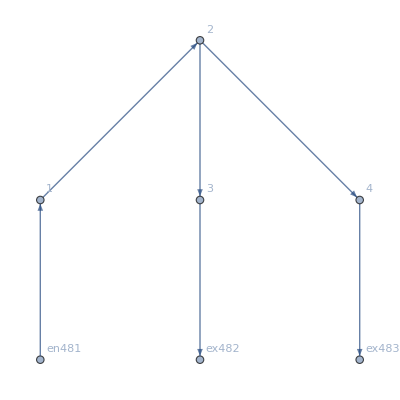

current: <|{1,1->2}→0,{1,en481->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex482}→0,{4,2->4}→0,{4,4->ex483}→0,{en481,en481->1}→0,{ex482,3->ex482}→1,{ex483,4->ex483}→0|>

transition: <|{1,1->2,en481->1}→0,{1,en481->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex482}→1,{3,3->ex482,2->3}→0,{4,2->4,4->ex483}→0,{4,4->ex483,2->4}→0|>

value: <|{1,1->2}→5,{1,en481->1}→5,{2,1->2}→4,{2,2->3}→1,{2,2->4}→1,{3,2->3}→0,{3,3->ex482}→0,{4,2->4}→1,{4,4->ex483}→1,{en481,en481->1}→5,{ex482,3->ex482}→0,{ex483,4->ex483}→1|>

```mathematica
Data=DataG[t];
(MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)1(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)3,S2->(*S123*)3,S3->3,S4->3,S5->0,S6->0}];)//Timing
If[MFGEquations =!= Null,
Print[MFGEquations["FG"]];
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
]
```

#### Non-linear case

```mathematica
alpha = .1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j484-j490-u508+u514==0.414128&&j485-j491-u509+u515==0.414128&&j486-j492-u510+u516==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j484-j490-u508+u514==0.414128&&j485-j491-u509+u515==0.414128&&j486-j492-u510+u516==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j484→1,j485→1.,j486→0.,j487→1.,j488→0.,j489→1,j490→0,j491→0,j492→0,j493→0,j494→0,j495→0,jt496→0,jt497→1,jt498→1.,jt499→0.,jt500→0,jt501→0,jt502→0,jt503→0,jt504→1.,jt505→0,jt506→0.,jt507→0,u508→4.17174,u509→0.585872,u510→0.585872,u511→0,u512→1,u513→4.17174,u514→3.58587,u515→0.,u516→0.585872,u517→0,u518→1,u519→4.17174|>

### New idea: U depends on the association from DataToEquations, together with the result of some nonlinear case

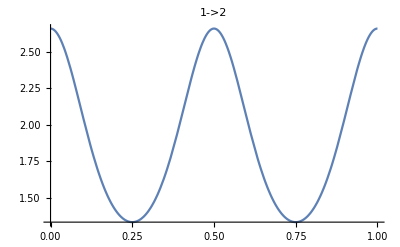
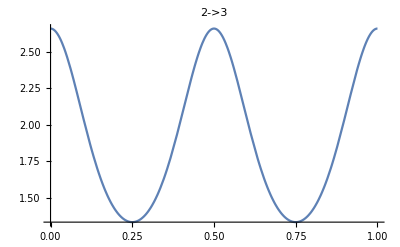
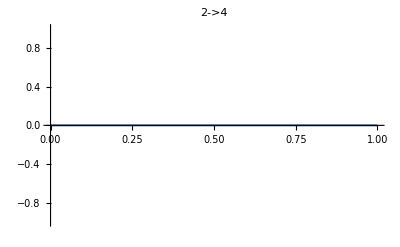

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

We need to fix what happens when the current is zero... think of what the U should be!

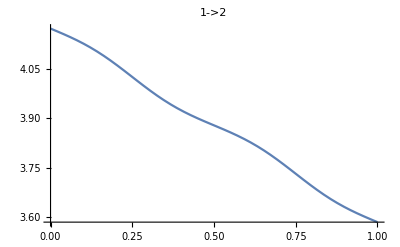
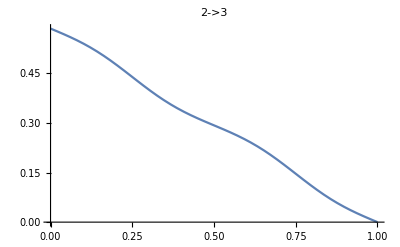
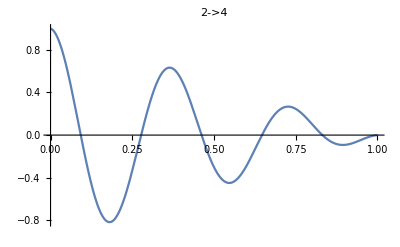

```mathematica
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

### Comparison between U and the linear function: U is not linear, if alpha =!=1 !

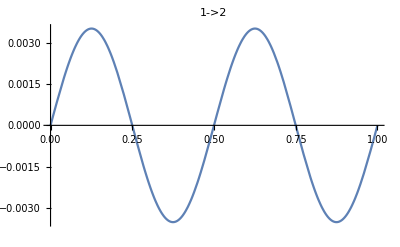
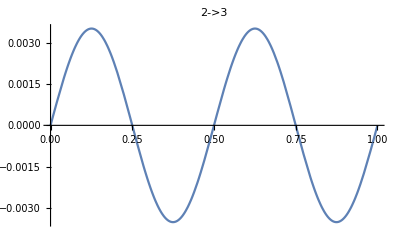
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
coeff = AssociationThread[MFGEquations["BEL"],(U[1,#,MFGEquations/.FFR]-U[0,#,MFGEquations/.FFR])&/@MFGEquations["BEL"]];
start = AssociationThread[MFGEquations["BEL"],(U[0,#,MFGEquations/.FFR])&/@MFGEquations["BEL"]];
Plot[U[x, #, MFGEquations/.FFR]-(start[#]+x*coeff[#]),{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```